## Shallow Flow Moment Equations (periodic in x)

## Function Definitions

### Tools

```mathematica
Clear["Global`*"]

SetAttributes[{P,A0},Listable]
ZeroMatrix[n_]:=0IdentityMatrix[n]
Diag[list_]:=DiagonalMatrix[list]

interpolate[pts_,val_,dim_]:=Block[{len=Length[Flatten[val]]},
Interpolation[ArrayReshape[Flatten[Thread[{ArrayReshape[Flatten[pts],{len,dim}],Flatten[val]}]],{len,dim+1}],InterpolationOrder->1]
]
iSize=400;
color={Red,Green,Blue,Purple};
markers={▲,■,◆,●,★};
```

### Cell Interface Reconstruction

```mathematica
gam=1.5;
Rlimit[dm_,dp_]=If[dp dm≤0,0,Sign[dp]Min[Abs[gam dm],Abs[(2dp+dm)/3],Abs[(1+gam)/2 dp]]]; (*Limiter*)
Rfull[dm_,dp_]=Sign[dp]Max[0,Min[Sign[dp](2dp+dm)/3,Max[-Sign[dp]dm,Min[gam Sign[dp]dm,Sign[dp](2dp+dm)/3,(1+gam)/2 Abs[dp]]]]];

Recon[list_,opt_]:=Map[Map[Function[{um,u,up},{u+1/2 Rlimit[u-um,up-u],u-1/2 Rlimit[up-u,u-um]}]@@#&,Partition[ArrayPad[#,2,opt,InterpolationOrder->1],3,1]]&,list]
```

### Full Grid Flux Calculation

```mathematica
Residuum[U_]:=Block[{Urecons1,Uright1,Uleft1,CMax,delta=0.95},
Urecons=Recon[U,"Periodic"];

Uright=Urecons⟦All,;;-2,1⟧;
Uleft=Urecons⟦All,2;;,2⟧;
dU=Uright⟦All,2;;⟧-Uleft⟦All,;;-2⟧;

CMax=ConstantArray[ListConvolve[{1/2,1/2},MaxSpeed@@U,{1,-1},"Periodic"],Length[U]];
cMax=Max[CMax];

-1/dx Differences[1/2(Flux@@Uright+Flux@@Uleft)+delta/2 CMax(Uright-Uleft),{0,1}]+1/dx Transpose[MapThread[#1.#2&,{A0@@U,Transpose[dU]}]]-Transpose[P@@U]
]
```

### Simulation Setup and Time Integration

```mathematica
FiniteVolumeRun[nx_,tend_]:=Block[{H1,HU1,H2,HU2},
dx=(x2-x1)/nx;
xs[i_]=x1+(i-0.5)dx;

pts=Table[xs[i],{i,1,nx}];

Uraw=Transpose[Table[init[xs[i]],{i,1,nx}]];

cMax=0.0;
dt=0.1dx;
time=0.0;
step=0;

While[time<tend,

U1=Uraw+dt Residuum[Uraw];

U2=3/4 Uraw+1/4(U1+dt Residuum[U1]);

Uraw=1/3 Uraw+2/3(U2+dt Residuum[U2]);

time+=dt;
step++;

dt=0.995dx/cMax;
CFL=cMax dt/dx;
If[time+dt≥tend&&time<tend,dt=tend-time+10^-8];
];

{time,step}
];
```

### Visualization for Dynamic Output

```mathematica
Visual[U_,iSize_]:=Block[{nx,ny},

Grid[{{
Show[Plot[0,{x,x1,x2},PlotLabel->"h(x,t) at time: "<>ToString[time]<>" (step: "<>ToString[step]<>", Δt = "<>ToString[dt]<>", CFL = "<>ToString[CFL]<>")",PlotRange->{{x1,x2},{0.8,1.5}},Frame->True,ImageSize->iSize,Epilog->{Inset[Panel[modeltag],Scaled[{.9,.9}]]}],
ListPlot[Transpose[{pts,U⟦1⟧}],ImageSize->iSize]],
Show[Plot[{0},{x,x1,x2},PlotStyle->{Red,Blue,Green},PlotLabel->"u_Ave(x,t)",PlotRange->{{x1,x2},{-0.4,0.6}},Frame->True,ImageSize->iSize,Epilog->{Inset[Panel[modeltag],Scaled[{.9,.9}]]}],
ListPlot[Transpose[{pts,U⟦2⟧}],ImageSize->iSize]]}}]
]
```

## Reference Data from Depth-Projected Model

#### tend = 2.0

```mathematica
Kinematic†C={{-0.975,1.000853,0.250037,0,0},{-0.925,1.000929,0.250109,0,0},{-0.875,1.001096,0.250193,0,0},{-0.825,1.001377,0.250323,0,0},{-0.775,1.001855,0.250508,0,0},{-0.725,1.002618,0.250796,0,0},{-0.675,1.003865,0.251212,0,0},{-0.625,1.005833,0.25181,0,0},{-0.575,1.009016,0.25246,0,0},{-0.525,1.013448,0.253517,0,0},{-0.475,1.034466,0.23995,0,0},{-0.425,1.1902,0.101373,0,0},{-0.375,1.192672,0.111574,0,0},{-0.325,1.191692,0.126386,0,0},{-0.275,1.190442,0.143318,0,0},{-0.225,1.189408,0.161197,0,0},{-0.175,1.188645,0.180051,0,0},{-0.125,1.18797,0.199639,0,0},{-0.075,1.187465,0.219638,0,0},{-0.025,1.187242,0.239942,0,0},{0.025,1.187257,0.260183,0,0},{0.075,1.187601,0.280341,0,0},{0.125,1.187985,0.30032,0,0},{0.175,1.188602,0.319902,0,0},{0.225,1.189381,0.338897,0,0},{0.275,1.190534,0.356805,0,0},{0.325,1.191669,0.373468,0,0},{0.375,1.193444,0.389081,0,0},{0.425,1.189239,0.39772,0,0},{0.475,1.034302,0.260061,0,0},{0.525,1.013718,0.246737,0,0},{0.575,1.008959,0.247474,0,0},{0.625,1.005824,0.248177,0,0},{0.675,1.003849,0.24879,0,0},{0.725,1.002598,0.24921,0,0},{0.775,1.001829,0.249482,0,0},{0.825,1.001359,0.249665,0,0},{0.875,1.00108,0.249799,0,0},{0.925,1.000926,0.2499,0,0},{0.975,1.000855,0.249974,0,0}};
Kinematic†L={{-0.975,1.000965,0.249991,-0.083078,0.000032},{-0.925,1.001047,0.249972,-0.083044,0.000125},{-0.875,1.001248,0.249937,-0.082955,0.000226},{-0.825,1.001596,0.249873,-0.082811,0.000355},{-0.775,1.002148,0.249776,-0.08261,0.000525},{-0.725,1.003028,0.249606,-0.082349,0.00073},{-0.675,1.004416,0.249305,-0.082023,0.000978},{-0.625,1.006849,0.248524,-0.081669,0.001272},{-0.575,1.009483,0.248466,-0.081202,0.001598},{-0.525,1.063129,0.198193,-0.084438,0.00206},{-0.475,1.176315,0.091857,-0.092018,0.002894},{-0.425,1.17438,0.102789,-0.090372,0.003337},{-0.375,1.172107,0.115719,-0.088532,0.003726},{-0.325,1.169679,0.13044,-0.086604,0.004006},{-0.275,1.167704,0.146589,-0.08465,0.004117},{-0.225,1.166274,0.163888,-0.082762,0.004016},{-0.175,1.165348,0.182124,-0.081022,0.003663},{-0.125,1.164753,0.201079,-0.079567,0.002951},{-0.075,1.164436,0.22047,-0.078451,0.001952},{-0.025,1.164352,0.240107,-0.077816,0.0007},{0.025,1.164344,0.259912,-0.07779,-0.000729},{0.075,1.164484,0.279564,-0.078372,-0.002004},{0.125,1.164762,0.298948,-0.079555,-0.002969},{0.175,1.165321,0.317883,-0.081063,-0.003639},{0.225,1.166285,0.336109,-0.082804,-0.004008},{0.275,1.167687,0.353435,-0.084694,-0.004123},{0.325,1.169581,0.369623,-0.086642,-0.004007},{0.375,1.172035,0.384371,-0.088578,-0.003728},{0.425,1.174551,0.397045,-0.090465,-0.003338},{0.475,1.176503,0.406938,-0.092143,-0.0029},{0.525,1.064763,0.30375,-0.084962,-0.002067},{0.575,1.010174,0.252279,-0.081266,-0.001588},{0.625,1.006757,0.251408,-0.081663,-0.001267},{0.675,1.004407,0.250698,-0.082026,-0.000975},{0.725,1.003017,0.250389,-0.08235,-0.000725},{0.775,1.002135,0.250218,-0.082612,-0.000519},{0.825,1.001588,0.250131,-0.082811,-0.000353},{0.875,1.00124,0.250067,-0.082955,-0.000223},{0.925,1.001047,0.250032,-0.083039,-0.000122},{0.975,1.000968,0.250012,-0.083073,-0.000046}};
Kinematic†Q={{-0.975,1.000948,0.250015,0,-0.049753},{-0.925,1.001079,0.250022,0,-0.049629},{-0.875,1.001328,0.250025,0,-0.049448},{-0.825,1.001718,0.250023,0,-0.049211},{-0.775,1.002344,0.250022,0,-0.048869},{-0.725,1.003304,0.250016,0,-0.048433},{-0.675,1.004787,0.249973,0,-0.047906},{-0.625,1.007095,0.24985,0,-0.047281},{-0.575,1.010899,0.249314,0,-0.04659},{-0.525,1.017739,0.246905,0,-0.045922},{-0.475,1.173341,0.101805,0,-0.052492},{-0.425,1.183498,0.10182,0,-0.051121},{-0.375,1.181747,0.114826,0,-0.049278},{-0.325,1.18001,0.129923,0,-0.047572},{-0.275,1.178472,0.146461,0,-0.046129},{-0.225,1.177149,0.164153,0,-0.045111},{-0.175,1.175974,0.18274,0,-0.04462},{-0.125,1.174845,0.202012,0,-0.044946},{-0.075,1.17383,0.221705,0,-0.04583},{-0.025,1.172854,0.241662,0,-0.047306},{0.025,1.172028,0.26167,0,-0.049193},{0.075,1.171554,0.281569,0,-0.050888},{0.125,1.171517,0.30115,0,-0.052416},{0.175,1.171949,0.320267,0,-0.053725},{0.225,1.172901,0.338713,0,-0.054782},{0.275,1.174338,0.356265,0,-0.055618},{0.325,1.176273,0.372672,0,-0.056288},{0.375,1.178481,0.387248,0,-0.056818},{0.425,1.182098,0.401213,0,-0.057281},{0.475,1.152991,0.382371,0,-0.056372},{0.525,1.013658,0.251533,0,-0.050418},{0.575,1.008708,0.250517,0,-0.05023},{0.625,1.005388,0.249968,0,-0.050117},{0.675,1.003553,0.249885,0,-0.050051},{0.725,1.002419,0.249888,0,-0.050006},{0.775,1.001733,0.249917,0,-0.04997},{0.825,1.001302,0.249939,0,-0.049937},{0.875,1.001059,0.249962,0,-0.049917},{0.925,1.000942,0.249985,0,-0.049877},{0.975,1.00091,0.249999,0,-0.049815}};
Friction†R0p01†χINF†L={{-0.975,1.001013,0.250012,-0.069503,-9.*^-6},{-0.925,1.001073,0.250023,-0.069508,-0.000021},{-0.875,1.001229,0.25002,-0.069501,-0.000027},{-0.825,1.001504,0.250008,-0.069492,-0.000022},{-0.775,1.001956,0.249981,-0.069464,4.*^-6},{-0.725,1.002717,0.249907,-0.069395,0.000052},{-0.675,1.003964,0.249743,-0.069275,0.000128},{-0.625,1.006099,0.249312,-0.069102,0.000235},{-0.575,1.0092,0.248895,-0.068846,0.000365},{-0.525,1.030087,0.231577,-0.069569,0.000595},{-0.475,1.177082,0.093953,-0.078441,0.00143},{-0.425,1.177344,0.102033,-0.077156,0.001633},{-0.375,1.175115,0.114755,-0.075444,0.001791},{-0.325,1.172917,0.129684,-0.073483,0.001887},{-0.275,1.171253,0.145994,-0.071313,0.001895},{-0.225,1.170065,0.163441,-0.069015,0.001789},{-0.175,1.169346,0.181795,-0.066682,0.00156},{-0.125,1.169052,0.200881,-0.064519,0.001216},{-0.075,1.168891,0.220321,-0.062799,0.000742},{-0.025,1.168933,0.240119,-0.061808,0.00024},{0.025,1.168917,0.259918,-0.061762,-0.000251},{0.075,1.168929,0.279699,-0.062827,-0.000783},{0.125,1.169,0.299149,-0.064547,-0.001213},{0.175,1.169368,0.318227,-0.066685,-0.00156},{0.225,1.170054,0.336551,-0.06901,-0.001792},{0.275,1.171248,0.354034,-0.071336,-0.001894},{0.325,1.172895,0.370334,-0.073532,-0.001884},{0.375,1.175167,0.385179,-0.075503,-0.001782},{0.425,1.177695,0.398134,-0.077251,-0.001625},{0.475,1.175885,0.404946,-0.07858,-0.001406},{0.525,1.032337,0.270723,-0.06991,-0.000609},{0.575,1.009485,0.25143,-0.068874,-0.00037},{0.625,1.006064,0.250677,-0.069106,-0.000233},{0.675,1.003957,0.250263,-0.069281,-0.000124},{0.725,1.002709,0.25009,-0.069398,-0.000048},{0.775,1.001948,0.250014,-0.069462,-1.*^-6},{0.825,1.001493,0.249989,-0.06949,0.000023},{0.875,1.001221,0.249979,-0.069501,0.000027},{0.925,1.001072,0.24998,-0.069502,0.000019},{0.975,1.001014,0.249995,-0.069496,6.*^-6}};
Friction†R0p1†χINF†L={{-0.975,1.000745,0.250081,-0.014672,0},{-0.925,1.000815,0.250238,-0.014725,1.*^-6},{-0.875,1.000989,0.250402,-0.014823,1.*^-6},{-0.825,1.001278,0.250594,-0.014936,2.*^-6},{-0.775,1.001757,0.25081,-0.015051,3.*^-6},{-0.725,1.002519,0.251077,-0.015158,3.*^-6},{-0.675,1.003745,0.251402,-0.015248,4.*^-6},{-0.625,1.005694,0.251792,-0.015319,5.*^-6},{-0.575,1.009131,0.251817,-0.015369,6.*^-6},{-0.525,1.012134,0.253823,-0.015361,6.*^-6},{-0.475,1.091582,0.182809,-0.016435,0.000024},{-0.425,1.190141,0.09929,-0.017888,0.000045},{-0.375,1.187681,0.112785,-0.017579,0.00004},{-0.325,1.186094,0.127659,-0.017074,0.000033},{-0.275,1.184429,0.144201,-0.016405,0.000027},{-0.225,1.182938,0.162079,-0.015649,0.000021},{-0.175,1.181889,0.180762,-0.014879,0.000015},{-0.125,1.181099,0.200118,-0.014217,1.*^-5},{-0.075,1.180533,0.219968,-0.013668,5.*^-6},{-0.025,1.180359,0.239909,-0.013406,2.*^-6},{0.025,1.180248,0.260121,-0.013433,-2.*^-6},{0.075,1.180622,0.280039,-0.013681,-5.*^-6},{0.125,1.181047,0.299928,-0.014232,-1.*^-5},{0.175,1.181948,0.319219,-0.014899,-0.000015},{0.225,1.182988,0.337995,-0.015642,-0.000022},{0.275,1.18445,0.355748,-0.016388,-0.000027},{0.325,1.186112,0.372485,-0.017077,-0.000033},{0.375,1.187691,0.387202,-0.017602,-0.00004},{0.425,1.190872,0.401345,-0.017923,-0.000046},{0.475,1.090695,0.316334,-0.016521,-0.000024},{0.525,1.013282,0.247404,-0.015381,-6.*^-6},{0.575,1.008978,0.248039,-0.015371,-5.*^-6},{0.625,1.005661,0.248202,-0.015322,-5.*^-6},{0.675,1.003726,0.248597,-0.015249,-4.*^-6},{0.725,1.002506,0.248909,-0.015158,-3.*^-6},{0.775,1.001749,0.249189,-0.015051,-3.*^-6},{0.825,1.001271,0.249402,-0.01493,-2.*^-6},{0.875,1.000982,0.249597,-0.014816,-1.*^-6},{0.925,1.000809,0.249765,-0.014726,-1.*^-6},{0.975,1.000749,0.24992,-0.014674,0}};
Friction†R0p1†χ0p1†L={{-0.975,1.021344,0.17975,-0.039999,-0.006141},{-0.925,1.021193,0.180371,-0.040507,-0.006173},{-0.875,1.021207,0.181,-0.04103,-0.006213},{-0.825,1.02143,0.181658,-0.041566,-0.006267},{-0.775,1.021946,0.182358,-0.04212,-0.006341},{-0.725,1.022874,0.183122,-0.042695,-0.006438},{-0.675,1.024407,0.183951,-0.043297,-0.006562},{-0.625,1.026914,0.184731,-0.043934,-0.006714},{-0.575,1.030858,0.185293,-0.044603,-0.006885},{-0.525,1.035274,0.186667,-0.045315,-0.00709},{-0.475,1.099235,0.132495,-0.047853,-0.006944},{-0.425,1.141973,0.102675,-0.048007,-0.00573},{-0.375,1.149156,0.108299,-0.046992,-0.005142},{-0.325,1.154991,0.116501,-0.046226,-0.004986},{-0.275,1.159212,0.127332,-0.045569,-0.005093},{-0.225,1.162769,0.139724,-0.044978,-0.005377},{-0.175,1.165904,0.153215,-0.044463,-0.005749},{-0.125,1.168771,0.167477,-0.043905,-0.006162},{-0.075,1.171374,0.182228,-0.043693,-0.006553},{-0.025,1.173827,0.19725,-0.043589,-0.006965},{0.025,1.176158,0.212366,-0.043433,-0.007378},{0.075,1.178382,0.227316,-0.043418,-0.00774},{0.125,1.180513,0.241909,-0.043314,-0.008066},{0.175,1.182429,0.255951,-0.043113,-0.008308},{0.225,1.184131,0.269053,-0.0428,-0.008409},{0.275,1.18524,0.280771,-0.042286,-0.008288},{0.325,1.185528,0.290894,-0.041463,-0.00782},{0.375,1.169834,0.285362,-0.039695,-0.006644},{0.425,1.046125,0.174398,-0.035041,-0.005085},{0.475,1.037785,0.171442,-0.035265,-0.005194},{0.525,1.033374,0.171666,-0.035686,-0.005334},{0.575,1.03035,0.172457,-0.03614,-0.005472},{0.625,1.02814,0.173417,-0.036586,-0.005599},{0.675,1.026461,0.174394,-0.037012,-0.005713},{0.725,1.02516,0.175327,-0.037414,-0.005815},{0.775,1.024123,0.176198,-0.037796,-0.005904},{0.825,1.023286,0.177006,-0.038181,-0.005978},{0.875,1.022604,0.177756,-0.038592,-0.006036},{0.925,1.022058,0.178454,-0.039036,-0.006078},{0.975,1.021638,0.179115,-0.039507,-0.006111}};
Friction†R0p01†χ0p01†L={{-0.975,1.008663,0.238434,-0.074928,-0.003519},{-0.925,1.008514,0.23876,-0.075113,-0.003691},{-0.875,1.008489,0.239081,-0.075293,-0.003858},{-0.825,1.008617,0.239396,-0.075469,-0.004022},{-0.775,1.008945,0.239708,-0.075657,-0.004181},{-0.725,1.009568,0.240013,-0.075864,-0.004339},{-0.675,1.01065,0.240296,-0.076083,-0.004504},{-0.625,1.012466,0.240495,-0.076322,-0.00468},{-0.575,1.015869,0.240028,-0.076612,-0.004861},{-0.525,1.018219,0.241884,-0.076784,-0.005066},{-0.475,1.111198,0.155504,-0.083152,-0.00493},{-0.425,1.156513,0.121041,-0.084426,-0.003601},{-0.375,1.159454,0.129098,-0.082836,-0.003006},{-0.325,1.161791,0.139515,-0.081246,-0.002777},{-0.275,1.163443,0.152446,-0.079551,-0.002815},{-0.225,1.164868,0.166914,-0.077815,-0.003055},{-0.175,1.166285,0.182592,-0.076124,-0.003466},{-0.125,1.167677,0.199112,-0.074604,-0.00402},{-0.075,1.16889,0.216258,-0.073748,-0.004827},{-0.025,1.170132,0.233759,-0.073165,-0.005581},{0.025,1.171328,0.251431,-0.073109,-0.006113},{0.075,1.172444,0.269088,-0.073656,-0.006521},{0.125,1.173646,0.286557,-0.074496,-0.006782},{0.175,1.174901,0.303631,-0.075703,-0.006842},{0.225,1.176262,0.320119,-0.077151,-0.006747},{0.275,1.177769,0.335753,-0.078657,-0.00653},{0.325,1.179426,0.350262,-0.080126,-0.006189},{0.375,1.180922,0.3632,-0.081407,-0.005714},{0.425,1.182527,0.374563,-0.082366,-0.005067},{0.475,1.15641,0.358357,-0.081143,-0.003833},{0.525,1.026419,0.236996,-0.072351,-0.002459},{0.575,1.020598,0.235552,-0.072583,-0.002395},{0.625,1.016762,0.235282,-0.072904,-0.00238},{0.675,1.01434,0.235602,-0.07321,-0.002422},{0.725,1.01265,0.236031,-0.073493,-0.002514},{0.775,1.01143,0.236485,-0.073772,-0.002646},{0.825,1.010518,0.236927,-0.07404,-0.002806},{0.875,1.009828,0.237346,-0.074291,-0.002983},{0.925,1.009307,0.237735,-0.074524,-0.003164},{0.975,1.008924,0.238096,-0.074736,-0.003342}};
```

## Simulations "Run"

```mathematica
R=0.0;
χ=0.1;

x1=-1.0;
x2=1.0;

xOffset=0.5;
h0[x_]=1+Exp[3Cos[π (x+xOffset)]-4];
u0[x_]=0.25;
s0[x_]=-0.25;
κ0[x_]=0.0;
γ0[x_]=0.0;

nx=10;
tEnd=0.2;
```

### Time Evolution Output

```mathematica
show=True; 
Button[" Show/Hide ",show=!show,BaseStyle->{"GenericButton",12}]
Dynamic[
If[show,
If[Length[Uraw]>0,
Visual[Uraw,400],
"no data"
],""],SynchronousUpdating->True]
```

Show/Hide

### Classical Shallow Flow

```mathematica
modeltag="SW";
MaxSpeed[h_,hu_]=h^-1 Abs[hu]+√h;
Flux[h_,hu_]={hu,h^-1 hu^2+1/2 h^2};
P[h_,hu_]=Block[{u=h^-1 hu},R/χ{0,u}];
A0[h_,hu_]=Block[{},0IdentityMatrix[2]];
```

```mathematica
init[x_]={h0[x],h0[x]u0[x]};
FiniteVolumeRun[nx,tEnd];

hN0=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦1⟧,1,"Periodic"],1];
umN0=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦2⟧/Uraw⟦1⟧,1,"Periodic"],1];
```

### Level 1

```mathematica
modeltag="N = 1";
MaxSpeed[h_,hu_,hs_]=Block[{u=h^-1 hu,s=3 h^-1 hs},Abs[u]+√(h+s^2)];
Flux[h_,hu_,hs_]=Block[{u=h^-1 hu,s=3 h^-1 hs},{h u,h u^2+1/3 h s^2+1/2 h^2,2/3 h s u}];
P[h_,hu_,hs_]=Block[{u=h^-1 hu,s=3 h^-1 hs},R/χ{0,u+s,u+(1+4 χ/h)s}];
A0[h_,hu_,hs_]=Block[{u=h^-1 hu,s=3 h^-1 hs},{{0,0,0},{0,0,0},{0,0,1/3 u}}.Diag[{1,1,3}]];
```

```mathematica
init[x_]={h0[x],h0[x]u0[x],1/3 h0[x]s0[x]};
FiniteVolumeRun[nx,tEnd];

hN1=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦1⟧,1,"Periodic"],1];
umN1=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦2⟧/Uraw⟦1⟧,1,"Periodic"],1];
sN1=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[3Uraw⟦3⟧/Uraw⟦1⟧,1,"Periodic"],1];
```

### Level 2

```mathematica
modeltag="N = 2";
MaxSpeed[h_,hu_,hs_,hκ_]=Block[{u=h^-1 hu,s=3 h^-1 hs,κ=5 h^-1 hκ},Abs[u]+√(h+s^2)];
Flux[h_,hu_,hs_,hκ_]=Block[{u=h^-1 hu,s=3 h^-1 hs,κ=5 h^-1 hκ},{h u,h u^2+1/3 h s^2+1/5 h κ^2+1/2 h^2,2/3 h s u+4/15 h s κ,2/5 h u κ+2/15 h s^2+2/35 h κ^2}];
P[h_,hu_,hs_,hκ_]=Block[{u=h^-1 hu,s=3 h^-1 hs,κ=5 h^-1 hκ},R/χ{0,u+s+κ,u+(1+4 χ/h)s+κ,u+s+(1+12 χ/h)κ}];
A0[h_,hu_,hs_,hκ_]=Block[{u=h^-1 hu,s=3 h^-1 hs,κ=5 h^-1 hκ},{{0,0,0,0},{0,0,0,0},{0,0,(5u-κ)/15,s/15},{0,0,s/5,(7u+κ)/35}}.Diag[{1,1,3,5}]];
```

```mathematica
init[x_]={h0[x],h0[x]u0[x],1/3 h0[x]s0[x],1/5 h0[x]κ0[x]};
FiniteVolumeRun[nx,tEnd];

hN2=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦1⟧,1,"Periodic"],1];
umN2=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦2⟧/Uraw⟦1⟧,1,"Periodic"],1];
sN2=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[3Uraw⟦3⟧/Uraw⟦1⟧,1,"Periodic"],1];
κN2=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[5Uraw⟦4⟧/Uraw⟦1⟧,1,"Periodic"],1];
```

### Level 3

```mathematica
modeltag="N = 3";
MaxSpeed[h_,hu_,hs_,hκ_,hγ_]=Block[{u=h^-1 hu,s=3 h^-1 hs,κ=5 h^-1 hκ,γ=7 h^-1 hγ},Abs[u]+√(h+s^2)];
Flux[h_,hu_,hs_,hκ_,hγ_]=Block[{u=h^-1 hu,s=3 h^-1 hs,κ=5 h^-1 hκ,γ=7 h^-1 hγ},
{h u,
h u^2+1/3 h s^2+1/5 h κ^2+1/7 h γ^2+1/2 h^2,
2/3 h s u+4/15 h s κ+6/35 h γ κ,
2/5 h u κ+2/15 h s^2+6/35 h s γ+4/105 h γ^2+2/35 h κ^2,
2/7 h u γ+6/35 h s κ+8/105 h γ κ}];

P[h_,hu_,hs_,hκ_,hγ_]=Block[{u=h^-1 hu,s=3 h^-1 hs,κ=5 h^-1 hκ,γ=7 h^-1 hγ},
R/χ{0,u+s+κ+γ,u+(1+4 χ/h)s+κ+(1+4 χ/h)γ,u+s+(1+12 χ/h)κ+γ,u+(1+4 χ/h)s+κ+(1+24 χ/h)γ}];
A0[h_,hu_,hs_,hκ_,hγ_]=Block[{u=h^-1 hu,s=3 h^-1 hs,κ=5 h^-1 hκ,γ=7 h^-1 hγ},
{{0,0,0,0,0},{0,0,0,0,0},{0,0,u/3-κ/15,s/15-γ/35,κ/35},{0,0,s/5-(3 γ)/35,u/5+κ/35,(2 s)/35+γ/105},{0,0,(6 κ)/35,(4 s)/35+(2 γ)/105,u/7+κ/35}}.Diag[{1,1,3,5,7}]];
```

```mathematica
init[x_]={h0[x],h0[x]u0[x],1/3 h0[x]s0[x],1/5 h0[x]κ0[x],1/7 h0[x]γ0[x]};
FiniteVolumeRun[nx,tEnd];

hN3=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦1⟧,1,"Periodic"],1];
umN3=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦2⟧/Uraw⟦1⟧,1,"Periodic"],1];
sN3=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[3Uraw⟦3⟧/Uraw⟦1⟧,1,"Periodic"],1];
κN3=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[5Uraw⟦4⟧/Uraw⟦1⟧,1,"Periodic"],1];
```

## Comparison "Run"

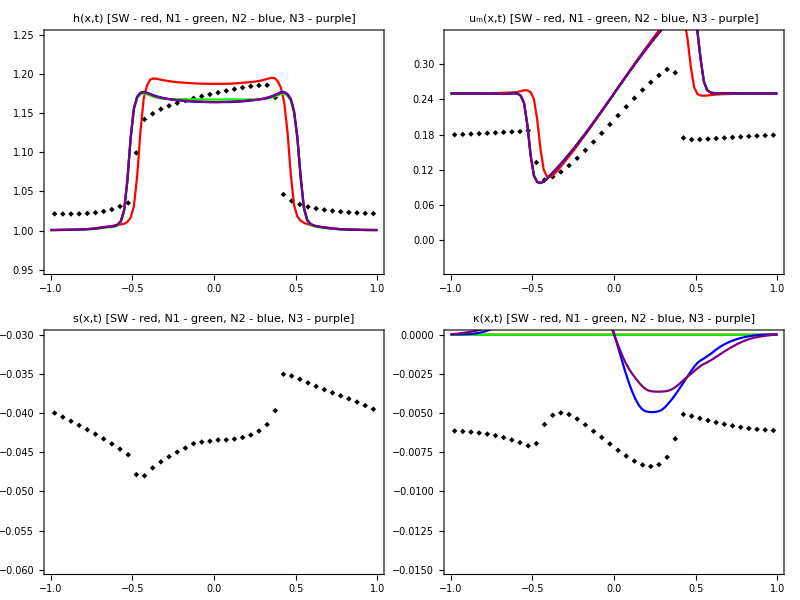

```mathematica
DataSet=Friction†R0p1†χ0p1†L;

Grid[{{Show[
ListPlot[{DataSet⟦All,{1,2}⟧},Joined->False,Frame->True,ImageSize->iSize,PlotStyle->{Black,Red,Black},PlotMarkers->{{markers⟦3⟧,Small},{markers⟦1⟧,Medium},{markers⟦3⟧,Medium}},PlotRange->{{-1,1},{0.95,1.25}}],
Plot[{hN0[x],hN1[x],hN2[x],hN3[x]},{x,-1,1},PlotStyle->color],PlotLabel->"h(x,t)   [SW - red, N1 - green, N2 - blue, N3 - purple]"],

Show[
ListPlot[{DataSet⟦All,{1,3}⟧},Joined->False,Frame->True,ImageSize->iSize,PlotStyle->{Black,Red,Black},PlotMarkers->{{markers⟦3⟧,Small},{markers⟦1⟧,Medium},{markers⟦3⟧,Medium}},PlotRange->{{-1,1},{-0.05,0.35}}],
Plot[{umN0[x],umN1[x],umN2[x],umN3[x]},{x,-1,1},PlotStyle->color],PlotLabel->"u_m(x,t)   [SW - red, N1 - green, N2 - blue, N3 - purple]"]},{

Show[
ListPlot[{DataSet⟦All,{1,4}⟧},Joined->False,Frame->True,ImageSize->iSize,PlotStyle->{Black,Red,Black},PlotMarkers->{{markers⟦3⟧,Small},{markers⟦1⟧,Medium},{markers⟦3⟧,Medium}},PlotRange->{{-1,1},{-0.06,-0.03}}],
Plot[{0,sN1[x]/3,sN2[x]/3,sN3[x]/3},{x,-1,1},PlotStyle->color],PlotLabel->"s(x,t)   [SW - red, N1 - green, N2 - blue, N3 - purple]"],

Show[
ListPlot[{DataSet⟦All,{1,5}⟧},Joined->False,Frame->True,ImageSize->iSize,PlotStyle->{Black,Red,Black},PlotMarkers->{{markers⟦3⟧,Medium},{markers⟦1⟧,Medium},{markers⟦3⟧,Medium}},PlotRange->{{-1,1},{-0.0,-0.015}}],
Plot[{0,0,κN2[x]/5,κN3[x]/5},{x,-1,1},PlotStyle->color,PlotRange->{{-1,1},All}],PlotLabel->"κ(x,t)   [SW - red, N1 - green, N2 - blue, N3 - purple]"]}}]
```

## Testing

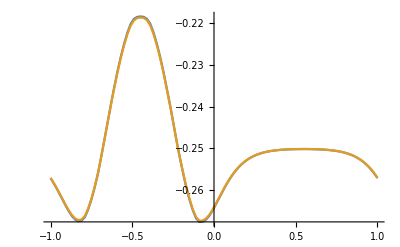

```mathematica
Plot[{sN1[x],sN2[x]},{x,-1,1}]
```